```mathematica
Needs["MFGraphs`"]
```

```mathematica
Get["/Users/ribeirrd/Dropbox/My Mac (kl-14835.kaust.edu.sa)/Documents/workspace/MFGraphs/MFGraphs/MFGraphs.m"](*Ricardo, use this when not running from eclipse.*)
```

```mathematica
Names["MFGraphs`*"]
```

{A,alpha,AtHead,AtTail,A$,beta,DataG,DataToEquations,EqEliminatorX,F,FixedPointSolverStepX,FixedSolverStepX2,g,g$2733,H,I1,I2,Intg,m,m$,n,OtherWay,p,Parameters,p$,S1,S10,S11,S12,S13,S14,S15,S16,S2,S3,S4,S5,S6,S7,S8,S9,StartSolverX,Test,TransitionsAt,triple2path,U1,U2,V,V$2733,W,W$2733,x,x$}

### Using the new functions in IterationFunction.m

```mathematica
Data=DataG[26];
MFGEquations=DataToEquations[Data];
```

DataToEquations: Finished assembling strucural equations:

EqEliminatorX: Reached a solution!

DataToEquations: Critical case ...

Something is wrong with the equations: 95-u617==0

DataToEquations: Reducing ...

Something is wrong with the equations: u617==95

DataToEquations: Done.

#### Non-linear case

```mathematica
MFGEquations["EqGeneralCase"]
```

95-u617==64.1073

```mathematica
KeySort[MFGEquations["criticalreduced"][[2]]]//Simplify
```

<|j607→80,j608→80,j609→80,j610→0,j611→0,j612→0,jt613→0,jt614→80,jt615→80,jt616→0,u618→15,u619→u617,u620→15,u621→15,u622→u617|>

```mathematica
MFGEquations["criticalreduced"][[2]]/.MFGEquations["criticalreduced"][[2]]
```

<|j609→80,u621→15,j607→80,j608→80,j610→0,j611→0,j612→0,jt613→0,jt614→80,jt615→80,jt616→0,u618→15,u622→u617,u619→u617,u620→15|>

```mathematica
FixedSolverStepX2[MFGEquations][MFGEquations["criticalreduced"][[2]]
]
```

Something is wrong with the equations: 95-u617==64.1073

Step: Reducing ...

Something is wrong with the equations: u617==30.8927

<|j609→80,u621→15,j607→80,j608→80,j610→0,j611→0,j612→0,jt613→0,jt614→80,jt615→80,jt616→0,u618→15,u622→u617,u619→u617,u620→15|>

```mathematica
MFGEquations["EqGeneralCase"]/.%
```

95-u617==64.1073

```mathematica
FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced"][[2]],10]
```

Something is wrong with the equations: 95-u617==64.1073

Step: Reducing ...

Something is wrong with the equations: u617==30.8927

<|j609→80,u621→15,j607→80,j608→80,j610→0,j611→0,j612→0,jt613→0,jt614→80,jt615→80,jt616→0,u618→15,u622→u617,u619→u617,u620→15|>

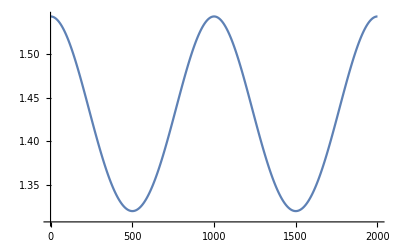

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.